We compute electron star profiles and free energy using the equations presented in [arXiv:2602.10460]. We tune two core thermodynamic parameters: the central temperature and the central chemical potential (T_0,μ_0). From these, we obtain different star profiles and identify the boundary thermodynamic parameters (T_∞,μ_∞) following the procedure explained in the paper.

The program is divided into three sections: 1. Computes profiles for a fixed pair of (T_0,μ_0); 2. Computes profiles by varying (T_0,μ_0) while keeping the ratio μ_0/T_0 constant; 3. Computes profiles at zero temperature (T_0=T_∞=0).

Parameters
- Physical (γ & mt): Fixed throughout the section execution, which can be modified to obtain profiles for different charged fluids.
- Numerical (order): The order of the polynomial expansion around r=0. The convergence radius of this expansion determines the initial values needed for NDSolve.

## 1. Electron Stars profiles with μ_0 & T_0 fixed

#### Parameters

```mathematica
μ0p=Rationalize[4]  ; (* chosen central chemical potential  *)
T0p=Rationalize[1.09] ; (* chosen central temperature  *)
mt=Rationalize[1] ; (* fluid parameter m̃ *)
γ=Rationalize[1] ;  (* fluid parameter γ *)

order=10 ; (* order of the background expansion  *)

precision=30  ; (* number of decimals we take in the numerical computations *)
```

### Background Computation

The first three sections compute the background using a power series expansion that starts at r=0 and extends up to r_i.  This obtained value of r_i is then used as the initial matching point for the numerical integration in the Star Profiles section, where the energy density profiles are computed and all the plots are shown. Finally, the last section, “Results”, displays the star profile where the power-law behavior can be observed; thus, this section can be run as a whole and then visualize the key findings in the last subsection.

#### Series

```mathematica
(* Power series expansion of the functions to be solved (using the boundary conditions to have a soft solution at r=0) *)
sM[r_]=Sum[m[n] r^n,{n,3,order}]+O[r]^(order+1) ; 
sh[r_]=Sum[hc[n] r^n,{n,2,order}]+O[r]^(order+1) ; 
sχ[r_]=Sum[c[n] r^n,{n,2,order}]+O[r]^(order+1) ;
sf[r_]=Exp[sχ[r]](1-2 sM[r]/r+1/2 Exp[-sχ[r]] r^2 sh'[r]^2+r^2) //Simplify ;
sg[r_]=(1-2 sM[r]/r+1/2 Exp[-sχ[r]] r^2 sh'[r]^2+r^2)^-1 //Simplify ;
sEf[r_]=Exp[-sχ[r]/2]sh'[r] //Simplify ;
sμ[r_,μ0_]=(μ0+sh[r])/(√sf[r])  ;  (* Chemical potential (Klein relation with gauge field) *)
sT[r_,T0_]=T0/(√sf[r])  ;  (* Temperature (Tolman relation) *)

(* List of coefficients to be determined and powers of r *)
tpot=Table[r^n,{n,1,order}] ;
tcoef=Join[Table[m[n],{n,3,order}],Table[hc[n],{n,2,order}],Table[c[n],{n,2,order}]] ;
ttodo=Join[tcoef,tpot] ;

(* Energy density, Pressure and charge density expasions *)  
sρ[μ0_,T0_]:=Collect[γ ϵ^2 √(ϵ^2-1)(1/(Exp[(ϵ-sμ[r,μ0])/sT[r,T0]]+1)+1/(Exp[(ϵ+sμ[r,μ0])/sT[r,T0]]+1)) //Expand,ttodo,SetPrecision[NIntegrate[#,{ϵ,1,∞},AccuracyGoal->∞,Method->"LocalAdaptive"],precision]&] ;
sP[μ0_,T0_]:=Collect[γ/3(ϵ^2-1)^(3/2) (1/(Exp[(ϵ-sμ[r,μ0])/sT[r,T0]]+1)+1/(Exp[(ϵ+sμ[r,μ0])/sT[r,T0]]+1)) //Expand,ttodo,SetPrecision[NIntegrate[#,{ϵ,1,∞},AccuracyGoal->∞,Method->"LocalAdaptive"],precision]&] ;
sσ[μ0_,T0_]:=Collect[γ/mt ϵ √(ϵ^2-1)(1/(Exp[(ϵ-sμ[r,μ0])/sT[r,T0]]+1)-1/(Exp[(ϵ+sμ[r,μ0])/sT[r,T0]]+1)) //Expand, ttodo,SetPrecision[NIntegrate[#,{ϵ,1,∞},AccuracyGoal->∞,Method->"LocalAdaptive"],precision]&] ;
```

#### Coeficientes

```mathematica
(* To agilize, first we evaluate with the test values *)
sρv=sρ[μ0p,T0p] ;
sPv=sP[μ0p,T0p] ;
sσv=sσ[μ0p,T0p] ;

(* Equations to solve *)
ecu1=Normal[sM'[r]-(r^2/2(sρv +2r sEf[r] √sg[r] sσv))] ;
ecu2=Normal[sχ'[r]-(r sg[r](sPv+sρv))] ;
ecu3=Normal[sEf'[r]-(-2 sEf[r]/r+√sg[r] sσv)] ;

(* Table of coeffcients equations. We take until order-1 since is the lower order due to the derivatives *)
tecu1=Table[Coefficient[ecu1,tpot[[k]]]==0,{k,order-1}] ;
tecu2=Table[Coefficient[ecu2,tpot[[k]]]==0,{k,order-1}] ;
tecu3=Table[Coefficient[ecu3,tpot[[k]]]==0,{k,order-1}] ;
(* and for the coeficients of order r^0 *)
zero1={ecu1-Sum[tpot[[k]] Coefficient[ecu1,tpot[[k]]],{k,order-1}]==0} ; 
zero2={ecu2-Sum[tpot[[k]] Coefficient[ecu2,tpot[[k]]],{k,order-1}]==0} ;
zero3={ecu3-Sum[tpot[[k]] Coefficient[ecu3,tpot[[k]]],{k,order-1}]==0} ;

tecus=Join[tecu1,tecu2,tecu3,zero1,zero2,zero3] ;

(* Solution *)
rknown= {m[0]-> 0,m[1]->0,m[2]-> 0,hc[0]->0,c[0]-> 0,c[1]-> 0} ;
rbackground=Join[Flatten[NSolve[tecus,tcoef,WorkingPrecision->precision]],rknown]  ;
```

#### Initial Radius Evaluation

```mathematica
(* Separate coefficients m, c and q, then order each one from the last coefficient to the first, then take the last 2 coefficients of the serie *)
tcm=Take[Sort[Select[rbackground,(#[[2]]=!=0&&ToString[#[[1,0]]]== "m")&],#1[[1,1]]>#2[[1,1]]&],2] ;
tcc=Take[Sort[Select[rbackground,(#[[2]]=!=0&&ToString[#[[1,0]]]== "c")&],#1[[1,1]]>#2[[1,1]]&],2] ;
tch=Take[Sort[Select[rbackground,(#[[2]]=!=0&&ToString[#[[1,0]]]== "hc")&],#1[[1,1]]>#2[[1,1]]&],2] ;

(* From the last 2 coefficients of the series, we compute the converge radius of each expansion *)
qcm=Abs[tcm[[2,2]]/tcm[[1,2]]] ;  (* m[last-1]/m[last]*)
dcm=Abs[tcm[[1,1,1]]-tcm[[2,1,1]]] ;  (* [last]-([last-1]) *)
ϵm=qcm^(1/dcm) ;   (* coverge radius *)

qcc=Abs[tcc[[2,2]]/tcc[[1,2]]] ;  (* c[last-1]/c[last]*)
dcc=Abs[tcc[[1,1,1]]-tcc[[2,1,1]]] ; (* [last]-([last-1]) *)
ϵc=qcc^(1/dcc) ;   (* coverge radius *)

qch=Abs[tch[[2,2]]/tch[[1,2]]] ;  (* q[last-1]/q[last]*)
dch=Abs[tch[[1,1,1]]-tch[[2,1,1]]] ;  (* [last]-([last-1]) *)
ϵh=qch^(1/dch) ;   (* coverge radius *)

(* We define now Subscript[r, i] which will be the initial radius for the later numerical differential solution. 
We take the lower of the previous radius convergences, and divided by 100 to reduced the numerical uncertaintly  *)
ri=Min[ϵc,ϵm,ϵh]/100 

(* Polynomial expansions of the background functions *)
pχ[r_]=Normal[sχ[r]/.rbackground] ;
pM[r_]=Normal[sM[r]/.rbackground] ;
ph[r_]=Normal[sh[r]/.rbackground] ;
(* Evaluation of the initial values for later use *)
χi=SetPrecision[pχ[ri],precision] ;
Mi=SetPrecision[pM[ri],precision] ;
hi=SetPrecision[ph[ri],precision] ;
hpi=SetPrecision[ph'[ri],precision] ;
```

0.00050823008488529614186781523129

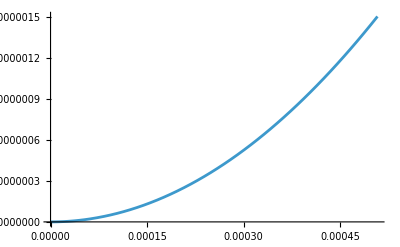

```mathematica
(* Visual test for some background *)
Plot[ph[r],{r,0,ri}]
```

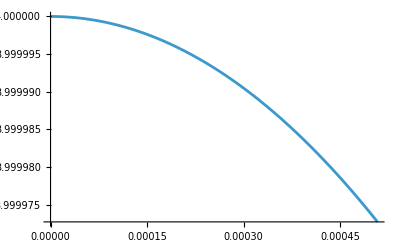

```mathematica
(* Visual test for some local chemical potential μ(r) *)
Plot[Evaluate[Normal[sμ[r,μ0p]/.rbackground]],{r,0,ri}]
```

#### Star Profiles

```mathematica
(* Electron star anzat *)
f[r_]=Exp[χ[r]](1-(2M[r])/r+1/2 Exp[-χ[r]] r^2 h'[r]^2+r^2)  ;
g[r_]=(1-(2M[r])/r+1/2 Exp[-χ[r]] r^2 h'[r]^2+r^2)^-1  ;
Ef[r_]= Exp[-χ[r]/2]h'[r]  ;
μ[r_]=(μ0p+h[r])/(√f[r]) ;    (* Local chemical potential definition *)
T[r_]=T0p/(√f[r]) ;  (* Temperature (from Tolman relation)  *)

(*ρ, P and σ integrals *)
ρ[μ_?NumericQ,T_?NumericQ]:=NIntegrate[SetPrecision[γ ϵ^2 √(ϵ^2-1)(1/(Exp[(ϵ-μ)/T]+1)+1/(Exp[(ϵ+μ)/T]+1)) ,precision],{ϵ,1,∞},AccuracyGoal->∞]
P[μ_?NumericQ,T_?NumericQ]:=NIntegrate[SetPrecision[γ/3(ϵ^2-1)^(3/2)(1/(Exp[(ϵ-μ)/T]+1)+1/(Exp[(ϵ+μ)/T]+1)),precision],{ϵ,1,∞},AccuracyGoal->∞]
σ[μ_?NumericQ,T_?NumericQ]:=NIntegrate[SetPrecision[γ/mt ϵ √(ϵ^2-1)(1/(Exp[(ϵ-μ)/T]+1)-1/(Exp[(ϵ+μ)/T]+1)) ,precision],{ϵ,1,∞},AccuracyGoal->∞]
rf=5 ;(* cut-off for the numerical solution *)
Solution=Flatten[NDSolve[{M'[r]== r^2/2(ρ[μ[r],T[r]]+2r Ef[r] √g[r] σ[μ[r],T[r]]),Ef'[r]==-2 Ef[r]/r+ √g[r] σ[μ[r],T[r]],χ'[r]== r g[r](P[μ[r],T[r]]+ρ[μ[r],T[r]]),M[ri]==Mi,χ[ri]==χi,h[ri]==hi,h'[ri]==hpi},{M,h,χ},{r,ri,rf},WorkingPrecision->precision],1];
```

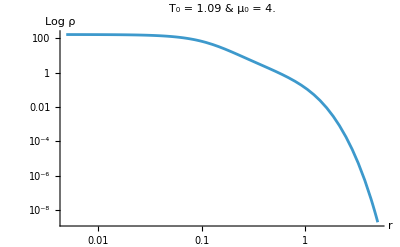

```mathematica
(* Full obtained density profiles (from r=0 to r=Subscript[r, f]) *)
ρfull=Piecewise[{{Normal[sρv]/.rbackground,0≤r≤ri},{Evaluate[ρ[μ[r],T[r]]/.Solution],ri<=r≤rf}}]  ;
(* we stop the numerical resolution if the Star density decays at least 10 order of magnitude at the cut-off Subscript[r, f]  *)
If[AnyTrue[(ρfull/.r->rf)/(ρfull/.r->0),#>10^-10&],"the cut-off r_f must be bigger"] 
(* PLOTS *)
LogLogPlot[Evaluate[ρfull],{r,0,rf},PlotLabel->"T_0 = "<>ToString[N[T0p]]<>" & μ_0 = "<>ToString[N[μ0p]],AxesLabel->{"r","Log ρ"},PlotRange->All]
```

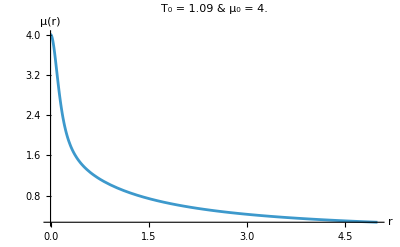

```mathematica
(* Full local chemical potential plots *)
Plot[Evaluate[Piecewise[{{Normal[sμ[r,μ0p]/.rbackground],0<=r≤ri},{μ[r]/.Solution,ri<r<=rf}}]],{r,0,rf},PlotLabel->"T_0 = "<>ToString[N[T0p]]<>" & μ_0 = "<>ToString[N[μ0p]],AxesLabel->{"r","μ(r)"},PlotRange->All]
```

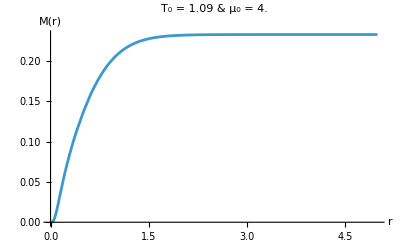

```mathematica
(* Full Mass profiles plots (from r=0 to r=Subscript[r, f]) *)
Plot[Evaluate[Piecewise[{{pM[r],0<=r≤ri},{Solution[[1,2]][r],ri<r<=rf}}]],{r,0,rf},PlotLabel->"T_0 = "<>ToString[N[T0p]]<>" & μ_0 = "<>ToString[N[μ0p]],AxesLabel->{"r","M(r)"},PlotRange->All]
```

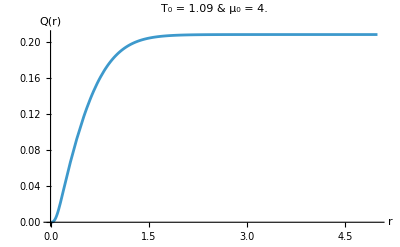

```mathematica
(* Full Charge profiles plots (from r=0 to r=Subscript[r, f]) *)
Plot[Evaluate[Piecewise[{{Exp[-pχ[r]/2]ph'[r] r^2,0<=r≤ri},{Exp[-χ[r]/2]h'[r] r^2/.Solution,ri<r<=rf}}]],{r,0,rf},PlotLabel->"T_0 = "<>ToString[N[T0p]]<>" & μ_0 = "<>ToString[N[μ0p]],AxesLabel->{"r","Q(r)"},PlotRange->All]
```

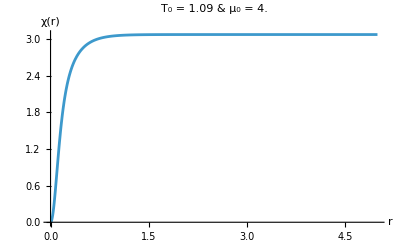

```mathematica
(* Full metric function χ(r) (from r=0 to r=Subscript[r, f]) *)
Plot[Evaluate[Piecewise[{{pχ[r],0<=r≤ri},{Solution[[3,2]][r],ri<r<=rf}}]],{r,0,rf},PlotLabel->"T_0 = "<>ToString[N[T0p]]<>" & μ_0 = "<>ToString[N[μ0p]],AxesLabel->{"r","χ(r)"},PlotRange->All]
```

```mathematica
(* Obtained mass Subscript[M, s], charge Subscript[Q, s] and Subscript[χ, s] of the Electron Star *)
Ms=M[rf]/.Solution  ; Qs=Exp[-χ[rf]/2]h'[rf] rf^2/.Solution  ; χs=χ[rf]/.Solution  ; 
(* Identifing the boundary chemical potential Subscript[μ, ∞] and temperature Subscript[T, ∞]  *)
h∞=D[r Solution[[2,2]][r],r]/.r->rf ;
μ∞=N[Exp[-χs/2](μ0p+h∞),precision] ; T∞=Exp[-χs/2]T0p  ;
HoldForm[{μ∞,T∞}]->{μ∞,T∞} //N
{μ0,T0}->{μ0p,T0p} //N
{μ0/T0,HoldForm[(μ∞)/(T∞)]}->{μ0p/T0p,(μ∞)/(T∞)} //N
{HoldForm[Subscript[T, ∞]^-1],-HoldForm[Subscript[M, s]]}->{(T∞)^-1,-Ms}//N
```

{μ∞,T∞}→{1.4111,0.234843}

{μ0,T0}→{4.,1.09}

{μ0/T0,(μ∞)/(T∞)}→{3.66972,6.00869}

{1/(T_∞),-1. M_s}→{4.25816,-0.232621}

#### Results

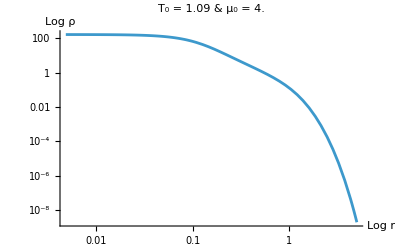

{μ0/T0,(μ∞)/(T∞)}→{3.66972,6.00869}

```mathematica
(* Full obtained density profiles (from r=0 to r=Subscript[r, f]) *)
ρfull=Piecewise[{{Normal[sρv]/.rbackground,0≤r≤ri},{Evaluate[ρ[μ[r],T[r]]/.Solution],ri<=r≤rf}}]  ;
(* PLOT *)
LogLogPlot[Evaluate[ρfull],{r,0,rf},PlotLabel->"T_0 = "<>ToString[N[T0p]]<>" & μ_0 = "<>ToString[N[μ0p]],AxesLabel->{"Log r","Log ρ"},PlotRange->All] 
(* Central ratio Subscript[μ, 0]/Subscript[T, 0] and obtained boundary ratio Subscript[μ, ∞]/Subscript[T, ∞] *)
{μ0/T0,HoldForm[(μ∞)/(T∞)]}->{μ0p/T0p,(μ∞)/(T∞)} //N
```

## 2. Electron Stars (μ_0/T_0 = constant)

#### Parameters

```mathematica
α=Rationalize[10]  ; (* chosen fixed ratio Subscript[μ, 0]/Subscript[T, 0]  *)
T0p=Table[Rationalize[i 10^-2],{i,9,13,0.25}] ; (* chosen central temperature values *)
T0p//N
NT0=Length[T0p] 
μ0p=Table[Rationalize[α T0p[[i]]],{i,NT0}]  ;
mt=Rationalize[1] ; (* fluid parameter m̃ *)
γ=Rationalize[1] ; (* fluid parameter γ *)

order=10 ; (* order of the background expansion  *)

precision=30  ; (* number of decimals we take in the numerical computations *)
```

{0.09,0.0925,0.095,0.0975,0.1,0.1025,0.105,0.1075,0.11,0.1125,0.115,0.1175,0.12,0.1225,0.125,0.1275,0.13}

17

### Background Computation

The first three sections compute the background using a power series expansion that starts at r=0 and extends up to r_i.  This obtained value of r_i is then used as the initial matching point for the numerical integration in the Star Profiles section, where the energy density profiles are computed. Finally, the last section displays the mass and charge profiles of the star.

#### Series

```mathematica
(* Power series expansion of the functions to be solved (using the boundary conditions to have a soft solution at r=0) *)
sM[r_]=Sum[m[n] r^n,{n,3,order}]+O[r]^(order+1) ; 
sh[r_]=Sum[hc[n] r^n,{n,2,order}]+O[r]^(order+1) ; 
sχ[r_]=Sum[c[n] r^n,{n,2,order}]+O[r]^(order+1) ;
sf[r_]=Exp[sχ[r]](1-2 sM[r]/r+1/2 Exp[-sχ[r]] r^2 sh'[r]^2+r^2) //Simplify ;
sg[r_]=(1-2 sM[r]/r+1/2 Exp[-sχ[r]] r^2 sh'[r]^2+r^2)^-1 //Simplify ;
sEf[r_]=Exp[-sχ[r]/2]sh'[r] //Simplify ;
sμ[r_,μ0_]=(μ0+sh[r])/(√sf[r])  ;  (* Chemical potential (Klein relation with gauge field) *)
sT[r_,T0_]=T0/(√sf[r])  ;  (* Temperature (Tolman relation) *)

(* List of coefficients to be determined and powers of r *)
tpot=Table[r^n,{n,1,order}] ;
tcoef=Join[Table[m[n],{n,3,order}],Table[hc[n],{n,2,order}],Table[c[n],{n,2,order}]] ;
ttodo=Join[tcoef,tpot] ;

(* Energy density, Pressure and charge density expasions *) 
sρ[μ0_,T0_]:=Collect[γ ϵ^2 √(ϵ^2-1)(1/(Exp[(ϵ-sμ[r,μ0])/sT[r,T0]]+1)+1/(Exp[(ϵ+sμ[r,μ0])/sT[r,T0]]+1)) //Expand,ttodo,SetPrecision[NIntegrate[#,{ϵ,1,∞},AccuracyGoal->∞,Method->"LocalAdaptive"],precision]&] ;
sP[μ0_,T0_]:=Collect[γ/3(ϵ^2-1)^(3/2) (1/(Exp[(ϵ-sμ[r,μ0])/sT[r,T0]]+1)+1/(Exp[(ϵ+sμ[r,μ0])/sT[r,T0]]+1)) //Expand,ttodo,SetPrecision[NIntegrate[#,{ϵ,1,∞},AccuracyGoal->∞,Method->"LocalAdaptive"],precision]&] ;
sσ[μ0_,T0_]:=Collect[γ/mt ϵ √(ϵ^2-1)(1/(Exp[(ϵ-sμ[r,μ0])/sT[r,T0]]+1)-1/(Exp[(ϵ+sμ[r,μ0])/sT[r,T0]]+1)) //Expand, ttodo,SetPrecision[NIntegrate[#,{ϵ,1,∞},AccuracyGoal->∞,Method->"LocalAdaptive"],precision]&] ;
```

#### Coeficients

```mathematica
(* To agilize, first we evaluate with the test values *)
sρv=Table[sρ[μ0p[[i]],T0p[[i]]],{i,NT0}] ;
sPv=Table[sP[μ0p[[i]],T0p[[i]]],{i,NT0}] ;
sσv=Table[sσ[μ0p[[i]],T0p[[i]]],{i,NT0}] ;

(* Equations to solve *)
ecu1=Table[Normal[sM'[r]-(r^2/2(sρv[[i]] +2 r sEf[r] √sg[r] sσv[[i]]))],{i,NT0}] ;
ecu2=Table[Normal[sχ'[r]-(r sg[r](sPv[[i]]+sρv[[i]]))],{i,NT0}] ;
ecu3=Table[Normal[sEf'[r]-(-2 sEf[r]/r+√sg[r] sσv[[i]])],{i,NT0}] ;

(* Table of coeffcients equations. We take until order-1 since is the lower order due to the derivatives *)
tecu1=Table[Table[Coefficient[ecu1[[i]],tpot[[k]]]==0,{k,order-1}],{i,NT0}] ;
tecu2=Table[Table[Coefficient[ecu2[[i]],tpot[[k]]]==0,{k,order-1}],{i,NT0}] ;
tecu3=Table[Table[Coefficient[ecu3[[i]],tpot[[k]]]==0,{k,order-1}],{i,NT0}] ;
(* and for the coeficients of order r^0 *)
zero1=Table[{ecu1[[i]]-Sum[tpot[[k]] Coefficient[ecu1[[i]],tpot[[k]]],{k,order-1}]==0},{i,NT0}] ; 
zero2=Table[{ecu2[[i]]-Sum[tpot[[k]] Coefficient[ecu2[[i]],tpot[[k]]],{k,order-1}]==0},{i,NT0}] ;
zero3=Table[{ecu3[[i]]-Sum[tpot[[k]] Coefficient[ecu3[[i]],tpot[[k]]],{k,order-1}]==0},{i,NT0}] ;

tecus=Table[Join[tecu1[[i]],tecu2[[i]],tecu3[[i]],zero1[[i]],zero2[[i]],zero3[[i]]],{i,NT0}] ;

(* Solution *)
rknown= Table[{m[0]-> 0,m[1]->0,m[2]-> 0,hc[0]->0,c[0]-> 0,c[1]-> 0},{i,NT0}] ;
rbackground=Table[Join[Flatten[NSolve[tecus[[i]],tcoef,WorkingPrecision->precision]],rknown[[i]]],{i,NT0}]  ;
```

#### Initial Radius Evaluation

```mathematica
(* Separate coefficients m, c and q, then order each one from the last coefficient to the first, then take the last 2 coefficients of the serie *)
tcm=Table[Take[Sort[Select[rbackground[[i]],(#[[2]]=!=0&&ToString[#[[1,0]]]== "m")&],#1[[1,1]]>#2[[1,1]]&],2],{i,NT0}] ;
tcc=Table[Take[Sort[Select[rbackground[[i]],(#[[2]]=!=0&&ToString[#[[1,0]]]== "c")&],#1[[1,1]]>#2[[1,1]]&],2],{i,NT0}] ;
tch=Table[Take[Sort[Select[rbackground[[i]],(#[[2]]=!=0&&ToString[#[[1,0]]]== "hc")&],#1[[1,1]]>#2[[1,1]]&],2],{i,NT0}] ;

(* From the last 2 coefficients of the series, we compute the converge radius of each expansion *)
qcm=Table[Abs[tcm[[i,2,2]]/tcm[[i,1,2]]],{i,NT0}] ;  (* m[last-1]/m[last]*)
dcm=Table[Abs[tcm[[i,1,1,1]]-tcm[[i,2,1,1]]],{i,NT0}] ;  (* [last]-([last-1]) *)
ϵm=Table[qcm[[i]]^(1/dcm[[i]]),{i,NT0}] ;   (* coverge radius *)

qcc=Table[Abs[tcc[[i,2,2]]/tcc[[i,1,2]]],{i,NT0}] ;  (* c[last-1]/c[last]*)
dcc=Table[Abs[tcc[[i,1,1,1]]-tcc[[i,2,1,1]]],{i,NT0}] ; (* [last]-([last-1]) *)
ϵc=Table[qcc[[i]]^(1/dcc[[i]]),{i,NT0}] ;   (* coverge radius *)

qch=Table[Abs[tch[[i,2,2]]/tch[[i,1,2]]],{i,NT0}] ;  (* q[last-1]/q[last]*)
dch=Table[Abs[tch[[i,1,1,1]]-tch[[i,2,1,1]]],{i,NT0}] ;  (* [last]-([last-1]) *)
ϵh=Table[qch[[i]]^(1/dch[[i]]),{i,NT0}] ;   (* coverge radius *)

(* We define now Subscript[r, i] which will be the initial radius for the later numerical differential solution. 
We take the lower of the previous radius convergences, and divided by 100 to reduced the numerical uncertaintly  *)
ri=Table[Min[ϵc[[i]],ϵm[[i]],ϵh[[i]]]/100,{i,NT0}] 

(* Polynomial expansions of the background functions *)
pχ[r_]=Table[Normal[sχ[r]/.rbackground[[i]]],{i,NT0}] ;
pM[r_]=Table[Normal[sM[r]/.rbackground[[i]]],{i,NT0}] ;
ph[r_]=Table[Normal[sh[r]/.rbackground[[i]]],{i,NT0}] ;
(* Evaluation of the initial values for later use *)
χi=SetPrecision[Table[pχ[ri[[i]]][[i]],{i,NT0}],precision] ;
Mi=SetPrecision[Table[pM[ri[[i]]][[i]],{i,NT0}],precision] ;
hi=SetPrecision[Table[ph[ri[[i]]][[i]],{i,NT0}],precision] ;
hpi=SetPrecision[Table[ph'[ri[[i]]][[i]],{i,NT0}],precision] ;
```

{0.00779362142229995974194847726732,0.00803377572135819901891872257626,0.00828251888237628420413480351823,0.00844454631578143505847584244987,0.00857394204440877100641398716647,0.00868161862516721794654986457112,0.00877126600560757402349882681106,0.00884780243431228966706576436628,0.00891593693569689388750447402457,0.00897939912686888703639555451312,0.00904078954715137353318941816085,0.00910175685122866247176867517498,0.00916327270782721180809789758897,0.00922586856128550741281783347218,0.00928981928273263842264900939785,0.00935522428484199857780565991898,0.009422099662286111474782167515}

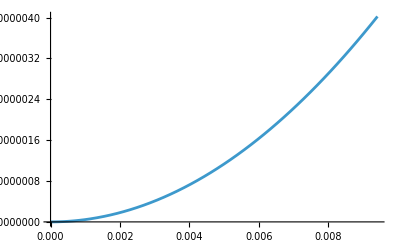

```mathematica
(* Visual test for some background *)
Plot[ph[r][[-1]],{r,0,ri[[-1]]}]
```

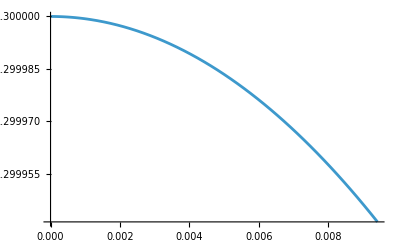

```mathematica
(* Visual test for some local chemical potential μ(r) *)
Plot[Evaluate[Normal[sμ[r,μ0p[[-1]]]/.rbackground[[-1]]]],{r,0,ri[[-1]]}]
```

#### Star Profiles

```mathematica
(* Electron star anzat *)
f[r_]=Exp[χ[r]](1-(2M[r])/r+1/2 Exp[-χ[r]] r^2 h'[r]^2+r^2)  ;
g[r_]=(1-(2M[r])/r+1/2 Exp[-χ[r]] r^2 h'[r]^2+r^2)^-1  ;
Ef[r_]= Exp[-χ[r]/2]h'[r]  ;
μ[r_]=Table[(μ0p[[i]]+h[r])/(√f[r]),{i,NT0}] ;   (* Local chemical potential definition *)
T[r_]=Table[T0p[[i]]/(√f[r]),{i,NT0}] ; (* Temperature (from Tolman relation)  *)
(*ρ, P and σ integrals *)
ρ[μ_?NumericQ,T_?NumericQ]:=NIntegrate[SetPrecision[γ ϵ^2 √(ϵ^2-1)(1/(Exp[(ϵ-μ)/T]+1)+1/(Exp[(ϵ+μ)/T]+1)) ,precision],{ϵ,1,∞},AccuracyGoal->∞]
P[μ_?NumericQ,T_?NumericQ]:=NIntegrate[SetPrecision[γ/3(ϵ^2-1)^(3/2)(1/(Exp[(ϵ-μ)/T]+1)+1/(Exp[(ϵ+μ)/T]+1)),precision],{ϵ,1,∞},AccuracyGoal->∞]
σ[μ_?NumericQ,T_?NumericQ]:=NIntegrate[SetPrecision[γ/mt ϵ √(ϵ^2-1)(1/(Exp[(ϵ-μ)/T]+1)-1/(Exp[(ϵ+μ)/T]+1)) ,precision],{ϵ,1,∞},AccuracyGoal->∞]
rf=10 ; (* cut-off for the numerical solution *)
Solution=Table[Flatten[NDSolve[{M'[r]== r^2/2(ρ[μ[r][[i]],T[r][[i]]]+2r Ef[r] √g[r] σ[μ[r][[i]],T[r][[i]]]),Ef'[r]==-2 Ef[r]/r+ √g[r] σ[μ[r][[i]],T[r][[i]]],χ'[r]== r g[r](P[μ[r][[i]],T[r][[i]]]+ρ[μ[r][[i]],T[r][[i]]]),M[ri[[i]]]==Mi[[i]],χ[ri[[i]]]==χi[[i]],h[ri[[i]]]==hi[[i]],h'[ri[[i]]]==hpi[[i]]},{M,h,χ},{r,ri[[i]],rf},WorkingPrecision->precision],1],{i,NT0}] ;
```

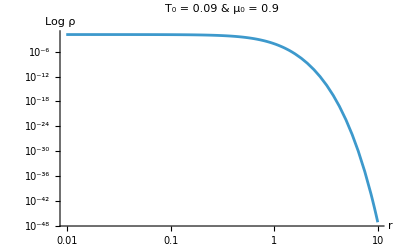
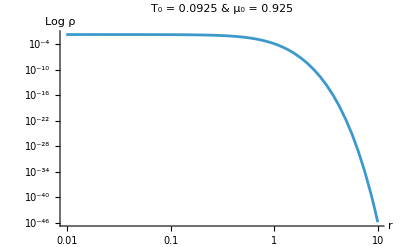
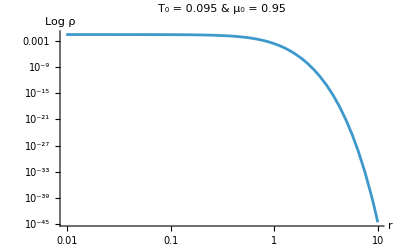
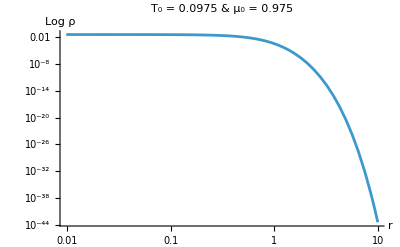
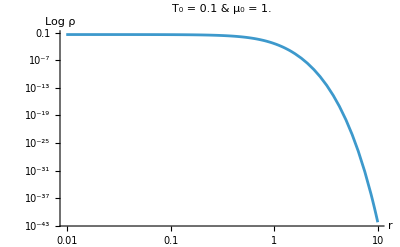
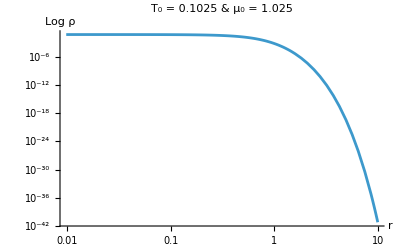
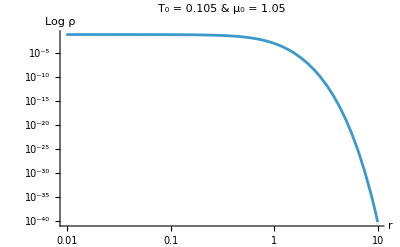
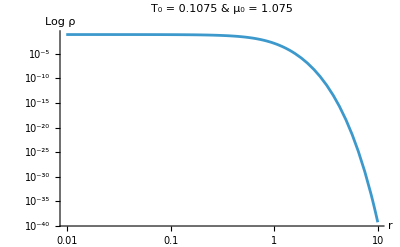

```mathematica
(* Full obtained density profiles (from r=0 to r=Subscript[r, f]) *)
ρfull=Table[Piecewise[{{Normal[sρv[[i]]]/.rbackground[[i]],0≤r≤ri[[i]]},{Evaluate[ρ[μ[r][[i]],T[r][[i]]]/.Solution[[i]]],ri[[i]]<=r≤rf}}],{i,NT0}]  ;
(* we stop the numerical resolution if the Star density decays at least 10 order of magnitude at the cut-off Subscript[r, f]  *)
If[AnyTrue[(ρfull/.r->rf)/(ρfull/.r->0),#>10^-10&],"the cut-off r_f must be bigger"] 
(* PLOTS *)
Table[LogLogPlot[Evaluate[ρfull[[i]]],{r,0,rf},PlotLabel->"T_0 = "<>ToString[N[T0p[[i]]]]<>" & μ_0 = "<>ToString[N[μ0p[[i]]]],AxesLabel->{"r","Log ρ"},PlotRange->All],{i,NT0}]
```

#### Mass & Charge plots

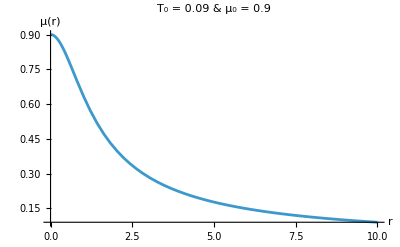
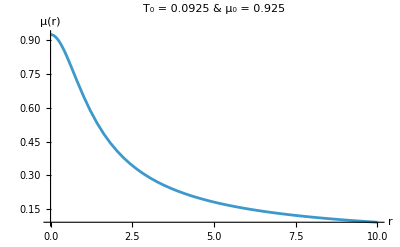
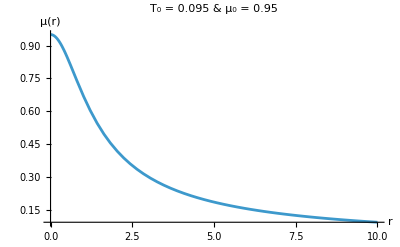
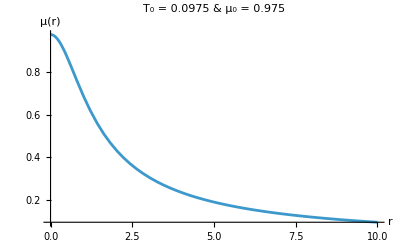
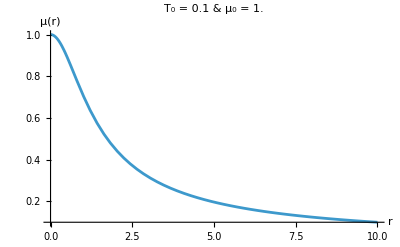
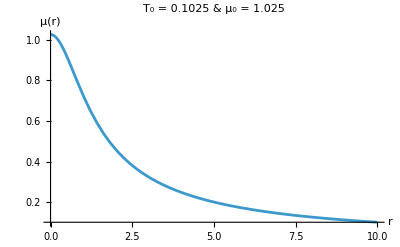
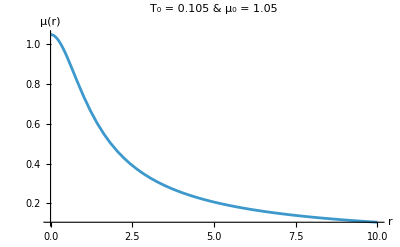
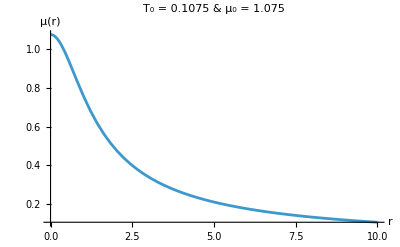

```mathematica
(* Full local chemical potential plots *)
Table[Plot[Evaluate[Piecewise[{{Normal[sμ[r,μ0p[[i]]]/.rbackground[[i]]],0<=r≤ri[[i]]},{μ[r][[i]]/.Solution[[i]],ri[[i]]<r<=rf}}]],{r,0,rf},PlotLabel->"T_0 = "<>ToString[N[T0p[[i]]]]<>" & μ_0 = "<>ToString[N[μ0p[[i]]]],AxesLabel->{"r","μ(r)"},PlotRange->All],{i,NT0}]
```

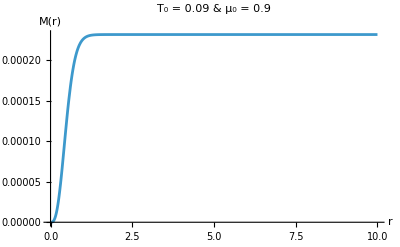
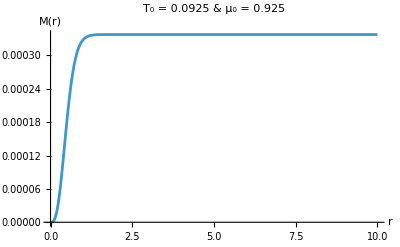
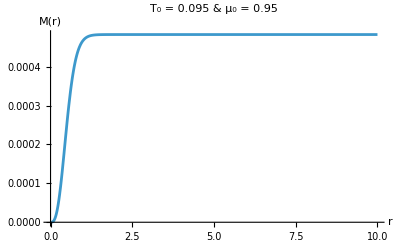
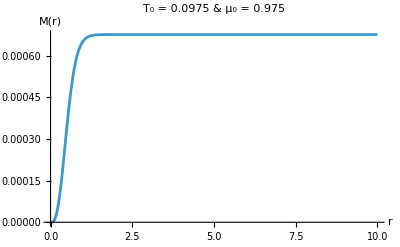
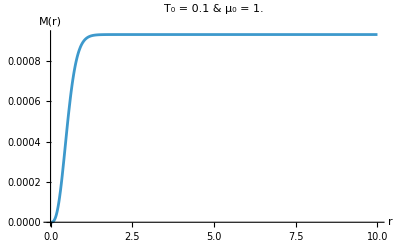
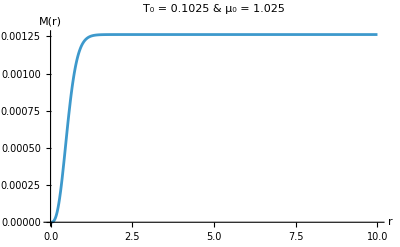
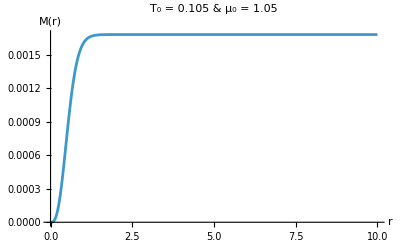
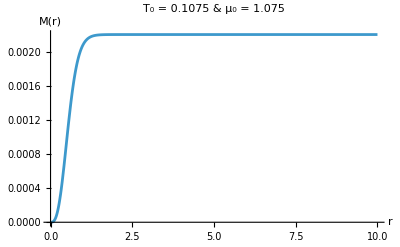

```mathematica
(* Full Mass profiles plots (from r=0 to r=Subscript[r, f]) *)
Table[Plot[Evaluate[Piecewise[{{pM[r][[i]],0<=r≤ri[[i]]},{Solution[[i,1,2]][r],ri[[i]]<r<=rf}}]],{r,0,rf},PlotLabel->"T_0 = "<>ToString[N[T0p[[i]]]]<>" & μ_0 = "<>ToString[N[μ0p[[i]]]],AxesLabel->{"r","M(r)"},PlotRange->All],{i,NT0}]
```

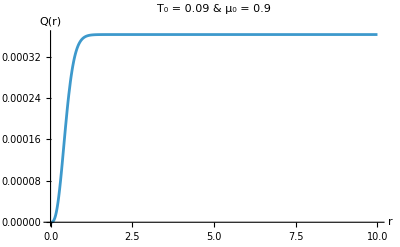
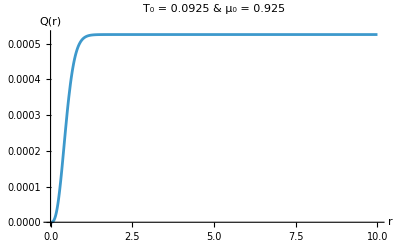
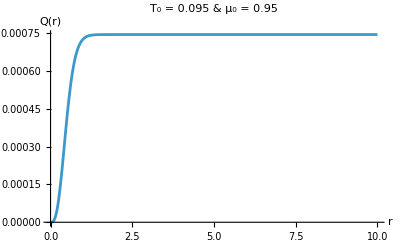
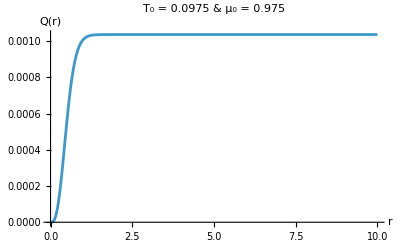
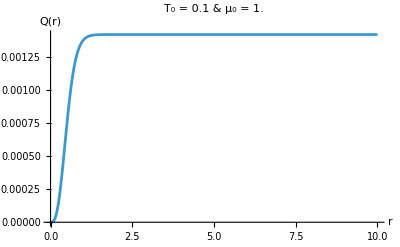
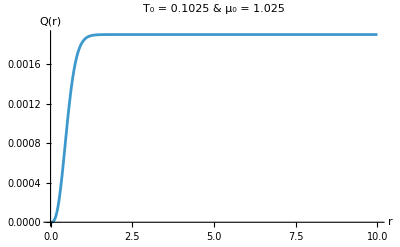
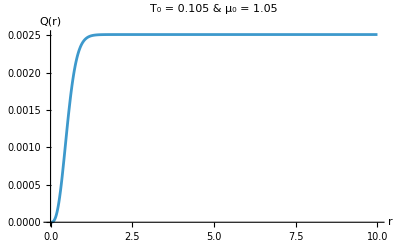
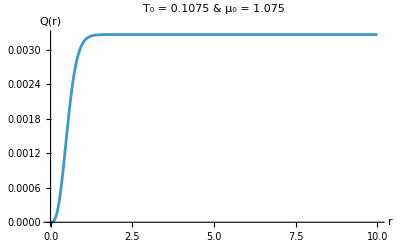

```mathematica
(* Full Charge profiles plots (from r=0 to r=Subscript[r, f]) *)
Table[Plot[Evaluate[Piecewise[{{Exp[-(pχ[r][[i]])/2]ph'[r][[i]] r^2,0<=r≤ri[[i]]},{Exp[-χ[r]/2]h'[r] r^2/.Solution[[i]],ri[[i]]<r<=rf}}]],{r,0,rf},PlotLabel->"T_0 = "<>ToString[N[T0p[[i]]]]<>" & μ_0 = "<>ToString[N[μ0p[[i]]]],AxesLabel->{"r","Q(r)"},PlotRange->All],{i,NT0}]
```

### Katz Plot

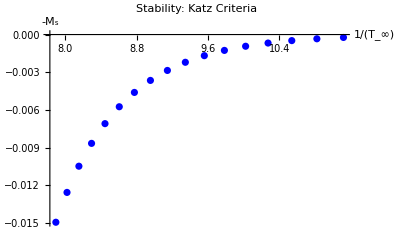

```mathematica
(* Obtained mass Subscript[M, s], charge Subscript[Q, s] and Subscript[χ, s] of the Electron Star *)
Ms=M[rf]/.Solution  ; Qs=Exp[-χ[rf]/2]h'[rf] rf^2/.Solution  ; χs=χ[rf]/.Solution  ; 
(* Identifing the boundary chemical potential Subscript[μ, ∞] and temperature Subscript[T, ∞]  *)
h∞=Table[D[r Solution[[i,2,2]][r],r]/.r->rf,{i,NT0}] ;
μ∞=N[Re[Table[Exp[-χs[[i]]/2](μ0p[[i]]+h∞[[i]]),{i,NT0}]],precision] ;  T∞=Table[Exp[-χs[[i]]/2]T0p[[i]],{i,NT0}]  ;
(* Plot of the Katz criteria *)
katz=Table[{1/(T∞[[i]]),-Ms[[i]]},{i,NT0}]  ;
ListPlot[katz,AxesLabel->{"1/(T_∞)","-M_s"},PlotRange->All,PlotLabel->"Stability: Katz Criteria",PlotLegends->"μ/T="<>ToString[N[α]],PlotStyle->Blue]
```

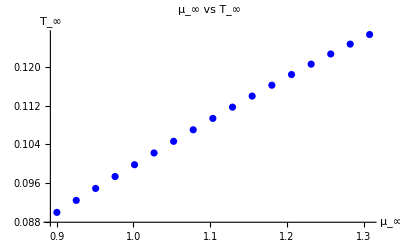

```mathematica
(* Relation between the chosen central chemical potential Subscript[μ, 0] and the obtained boundary chemical potential Subscript[μ, ∞] *)
ListPlot[Table[{μ∞[[i]],T∞[[i]]},{i,NT0}],AxesLabel->{"μ_∞","T_∞"},PlotRange->All,PlotLabel->"μ_∞ vs T_∞",PlotStyle->Blue]
```

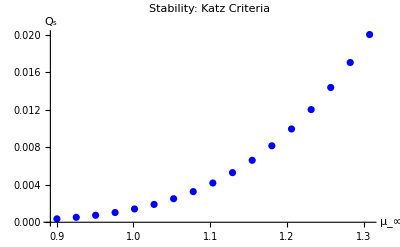

```mathematica
(* Plot of the Electron Star charge vs the chemical potential *)
katz2=Table[{μ∞[[i]],Qs[[i]]},{i,NT0}]  ;
ListPlot[katz2,AxesLabel->{"μ_∞","Q_s"},PlotRange->All,PlotLabel->"Stability: Katz Criteria",PlotLegends->"μ/T="<>ToString[N[α]],PlotStyle->Blue]
```

### Free Energy

```mathematica
(* Free energy of the Star *)
χfull=Table[Piecewise[{{pχ[r][[i]],0<=r≤ri[[i]]},{Solution[[i,3,2]][r],ri[[i]]<r<=rf}}],{i,NT0}] ;
hfull=Table[Piecewise[{{ph[r][[i]],0<=r≤ri[[i]]},{Solution[[i,2,2]][r],ri[[i]]<r<=rf}}],{i,NT0}] ;
gfull=Table[Piecewise[{{Normal[sg[r]]/.rbackground[[i]],0≤r≤ri[[i]]},{Evaluate[g[r]/.Solution[[i]]],ri[[i]]<=r≤rf}}],{i,NT0}]  ;
Pfull=Table[Piecewise[{{Normal[sPv[[i]]]/.rbackground[[i]],0≤r≤ri[[i]]},{Evaluate[P[μ[r][[i]],T[r][[i]]]/.Solution[[i]]],ri[[i]]<=r≤rf}}],{i,NT0}]  ;
σfull=Table[Piecewise[{{Normal[sσv[[i]]]/.rbackground[[i]],0≤r≤ri[[i]]},{Evaluate[σ[μ[r][[i]],T[r][[i]]]/.Solution[[i]]],ri[[i]]<=r≤rf}}],{i,NT0}]  ;
Ss=Table[4π NIntegrate[SetPrecision[r^2 (Exp[χfull[[i]]/2]((Pfull[[i]]+ρfull[[i]])/T0p[[i]])-√gfull[[i]]((μ0p[[i]]+hfull[[i]])/T0p[[i]])σfull[[i]]),precision],{r,0,rf}],{i,NT0}];
Wstar∞=Table[{T∞[[i]],4π (Exp[χs[[i]]/2](2Ms[[i]]-Qs[[i]]μ∞[[i]]))-T∞[[i]]Ss[[i]]},{i,NT0}]; 

(* Free energy of the Large BH *)
WBH∞[TBH_,μBH_]=FullSimplify[1/27 π (2 π TBH-√2 √(-6+8 π^2 TBH^2+3 μBH^2)) (4 π TBH+√2 √(-6+8 π^2 TBH^2+3 μBH^2))^2,{TBH>=0,μBH∈Reals}] ;
WBH∞data=Table[{T∞[[i]],WBH∞[T∞[[i]],μ∞[[i]]]},{i,NT0}] ;

(* Free energy of the TAdS *)
WAdST∞[TAdS_]=0 ;
```

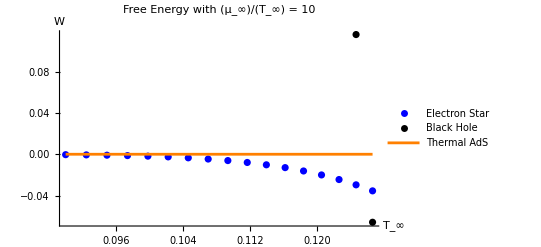

```mathematica
(* Plot of the Free energy of the Star, BH and TAdS, for the obtained values of the boundary chemical potential and temperature (Subscript[μ, ∞],Subscript[T, ∞]) *)
TBHi=TakeSmallest[Table[T∞[[i]],{i,NT0}],1][[1]] ; TBHf=TakeLargest[Table[T∞[[i]],{i,NT0}],1][[1]] ;
Show[ListPlot[{Wstar∞,WBH∞data},AxesLabel->{"T_∞","W"},PlotStyle->{Blue,Black},PlotRange->All,PlotLegends->{"Electron Star","Black Hole"},PlotLabel->"Free Energy with (μ_∞)/(T_∞) = "<>ToString[α,TraditionalForm]],Plot[WAdST∞[TBH],{TBH,TBHi,TBHf},PlotLegends->{"Thermal AdS"},PlotStyle->{Orange}],PlotRange->All]
```

## 3. Electron Stars at T = 0 (only particles)

#### Parameters

```mathematica
μ0p=Table[Rationalize[i],{i,1.35,1.5,0.01}] ;  (* chosen central chemical potential values *)
μ0p //N
Nμ0=Length[μ0p] 

mt=Rationalize[1] ;  (* fluid parameter m̃ *)
γ=Rationalize[1] ;   (* fluid parameter γ *)

order=10 ; (* order of the background expansion  *)

(* Energy and charge densities definitions (analytical). We only consider particles since at T=0 we can not have both particles and antiparticles (one is 0) *) 
ρf[μf_]=γ Simplify[Integrate[ϵ^2 √(ϵ^2-1),{ϵ,1,μf}],{μf>1}] ;
σf[μf_]=γ/mt Simplify[Integrate[ϵ √(ϵ^2-1),{ϵ,1,μf}],{μf>1}] ;
```

{1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5}

16

### Background Computation

The first three sections compute the background using a power series expansion that starts at r=0 and extends up to r_i.  This obtained value of r_i is then used as the initial matching point for the numerical integration in the Star Profiles section, where the energy density profiles are computed. Finally, the last section displays the mass and charge profiles of the star.

#### Series

```mathematica
(* Power series expansion of the functions to be solved (using the boundary conditions to have a soft solution at r=0) *)
sM[r_]=Sum[m[n] r^n,{n,3,order}]+O[r]^(order+1) ; 
sh[r_]=Sum[hc[n] r^n,{n,2,order}]+O[r]^(order+1) ; 
sχ[r_]=Sum[c[n] r^n,{n,2,order}]+O[r]^(order+1) ;
sf[r_]=Exp[sχ[r]](1-2 sM[r]/r+1/2 Exp[-sχ[r]] r^2 sh'[r]^2+r^2) //Simplify ;
sg[r_]=(1-2 sM[r]/r+1/2 Exp[-sχ[r]] r^2 sh'[r]^2+r^2)^-1 //Simplify ;
sEf[r_]=Exp[-sχ[r]/2]sh'[r] //Simplify ;
sμ[r_,μ0_]=(μ0+sh[r])/(√sf[r])  ;  (* Chemical potential (Klein relation with gauge field) *)

(* List of coefficients to be determined and powers of r *)
tpot=Table[r^n,{n,1,order}] ;
tcoef=Join[Table[m[n],{n,3,order}],Table[hc[n],{n,2,order}],Table[c[n],{n,2,order}]] ;
ttodo=Join[tcoef,tpot] ;

(* Energy and charge densities expasions (to agilize, we evaluate with the test values for future use) *) 
sρv=Table[Collect[ρf[sμ[r,μ0p[[i]]]],tpot],{i,Nμ0}] //Simplify ;  
sσv=Table[Collect[σf[sμ[r,μ0p[[i]]]],tpot],{i,Nμ0}] //Simplify ;
```

#### Coeficientes

```mathematica
(* Equations to solve *)
ecu1=Table[Normal[sM'[r]-(r^2/2(sρv[[i]] +2 r sEf[r] √sg[r] sσv[[i]]))],{i,Nμ0}] ;
ecu2=Table[Normal[sχ'[r]-(r sg[r](sμ[r,μ0p[[i]]]sσv[[i]]))],{i,Nμ0}] ;
ecu3=Table[Normal[sEf'[r]-(-2 sEf[r]/r+√sg[r] sσv[[i]])],{i,Nμ0}] ;

(* Table of coeffcients equations. We take until order-1 since is the lower order due to the derivatives *)
tecu1=Table[Table[Coefficient[ecu1[[i]],tpot[[k]]]==0,{k,order-1}],{i,Nμ0}] ;
tecu2=Table[Table[Coefficient[ecu2[[i]],tpot[[k]]]==0,{k,order-1}],{i,Nμ0}] ;
tecu3=Table[Table[Coefficient[ecu3[[i]],tpot[[k]]]==0,{k,order-1}],{i,Nμ0}] ;
(* and for the coeficients of order r^0 *)
zero1=Table[{ecu1[[i]]-Sum[tpot[[k]] Coefficient[ecu1[[i]],tpot[[k]]],{k,order-1}]==0},{i,Nμ0}] ; 
zero2=Table[{ecu2[[i]]-Sum[tpot[[k]] Coefficient[ecu2[[i]],tpot[[k]]],{k,order-1}]==0},{i,Nμ0}] ;
zero3=Table[{ecu3[[i]]-Sum[tpot[[k]] Coefficient[ecu3[[i]],tpot[[k]]],{k,order-1}]==0},{i,Nμ0}] ;

tecus=Table[Join[tecu1[[i]],tecu2[[i]],tecu3[[i]],zero1[[i]],zero2[[i]],zero3[[i]]],{i,Nμ0}] ;

(* Solution *)
rknown= Table[{m[0]-> 0,m[1]->0,m[2]-> 0,hc[0]->0,c[0]-> 0,c[1]-> 0},{i,Nμ0}] ;
rbackground=Table[Join[Flatten[NSolve[tecus[[i]],tcoef]],rknown[[i]]],{i,Nμ0}]  ;
```

#### Initial Radius Evaluation

```mathematica
(* Separate coefficients m, c and q, then order each one from the last coefficient to the first, then take the last 2 coefficients of the serie *)
tcm=Table[Take[Sort[Select[rbackground[[i]],(#[[2]]=!=0.&&ToString[#[[1,0]]]== "m")&],#1[[1,1]]>#2[[1,1]]&],2],{i,Nμ0}] ;
tcc=Table[Take[Sort[Select[rbackground[[i]],(#[[2]]=!=0.&&ToString[#[[1,0]]]== "c")&],#1[[1,1]]>#2[[1,1]]&],2],{i,Nμ0}] ;
tch=Table[Take[Sort[Select[rbackground[[i]],(#[[2]]=!=0.&&ToString[#[[1,0]]]== "hc")&],#1[[1,1]]>#2[[1,1]]&],2],{i,Nμ0}] ;

(* From the last 2 coefficients of the series, we compute the converge radius of each expansion *)
qcm=Table[Abs[tcm[[i,2,2]]/tcm[[i,1,2]]],{i,Nμ0}] ;  (* m[last-1]/m[last]*)
dcm=Table[Abs[tcm[[i,1,1,1]]-tcm[[i,2,1,1]]],{i,Nμ0}] ;  (* [last]-([last-1]) *)
ϵm=Table[qcm[[i]]^(1/dcm[[i]]),{i,Nμ0}] ;   (* coverge radius *)

qcc=Table[Abs[tcc[[i,2,2]]/tcc[[i,1,2]]],{i,Nμ0}] ;  (* c[last-1]/c[last]*)
dcc=Table[Abs[tcc[[i,1,1,1]]-tcc[[i,2,1,1]]],{i,Nμ0}] ; (* [last]-([last-1]) *)
ϵc=Table[qcc[[i]]^(1/dcc[[i]]),{i,Nμ0}] ;   (* coverge radius *)

qch=Table[Abs[tch[[i,2,2]]/tch[[i,1,2]]],{i,Nμ0}] ;  (* q[last-1]/q[last]*)
dch=Table[Abs[tch[[i,1,1,1]]-tch[[i,2,1,1]]],{i,Nμ0}] ;  (* [last]-([last-1]) *)
ϵh=Table[qch[[i]]^(1/dch[[i]]),{i,Nμ0}] ;   (* coverge radius *)

(* We define now Subscript[r, i] which will be the initial radius for the later numerical differential solution. 
We take the lower of the previous radius convergences, and divided by 100 to reduced the numerical uncertaintly  *)
ri=Table[Min[ϵc[[i]],ϵm[[i]],ϵh[[i]]]/100,{i,Nμ0}] 

(* Polynomial expansions of the background functions *)
pχ[r_]=Table[Normal[sχ[r]/.rbackground[[i]]],{i,Nμ0}] ;
pM[r_]=Table[Normal[sM[r]/.rbackground[[i]]],{i,Nμ0}] ;
ph[r_]=Table[Normal[sh[r]/.rbackground[[i]]],{i,Nμ0}] ;
(* Evaluation of the initial values for later use *)
χi=Table[pχ[ri[[i]]][[i]],{i,Nμ0}] ;
Mi=Table[pM[ri[[i]]][[i]],{i,Nμ0}] ;
hi=Table[ph[ri[[i]]][[i]],{i,Nμ0}] ;
hpi=Table[ph'[ri[[i]]][[i]],{i,Nμ0}] ;
```

{0.00935648,0.00938322,0.00941,0.00943684,0.00946371,0.00949063,0.00951757,0.00954453,0.0095715,0.00959846,0.00962539,0.00965228,0.0096791,0.00970583,0.00973244,0.0097589}

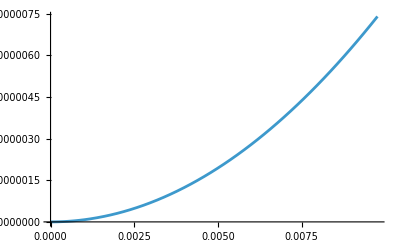

```mathematica
(* Visual test for some background *)
Plot[ph[r][[-1]],{r,0,ri[[-1]]}]
```

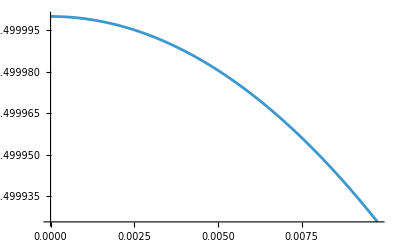

```mathematica
(* Visual test for some local chemical potential μ(r) *)
Plot[Evaluate[Normal[sμ[r,μ0p[[-1]]]/.rbackground[[-1]]]],{r,0,ri[[-1]]}]
```

#### Star Profiles

```mathematica
(* Electron star anzat *)
f[r_]=Exp[χ[r]](1-(2M[r])/r+1/2 Exp[-χ[r]] r^2 h'[r]^2+r^2)  ;
g[r_]=(1-(2M[r])/r+1/2 Exp[-χ[r]] r^2 h'[r]^2+r^2)^-1  ;
Ef[r_]= Exp[-χ[r]/2]h'[r]  ;
μ[r_]=Table[(μ0p[[i]]+h[r])/(√f[r]),{i,Nμ0}] ;   (* Local chemical potential definition *)
(*ρ, P and σ integrals *)
ρ[μf_?NumericQ]=HeavisideTheta[μf-1]ρf[μf]  ; 
σ[μf_?NumericQ]=HeavisideTheta[μf-1]σf[μf]  ; 

rf=2 ; (* cut-off for the numerical solution *)
Solution=Table[Flatten[NDSolve[{M'[r]== r^2/2(ρ[μ[r][[i]]]+2r Ef[r] √g[r] σ[μ[r][[i]]]),Ef'[r]==-2 Ef[r]/r+ √g[r] σ[μ[r][[i]]],χ'[r]== r g[r](μ[r][[i]]σ[μ[r][[i]]]),M[ri[[i]]]==Mi[[i]],χ[ri[[i]]]==χi[[i]],h[ri[[i]]]==hi[[i]],h'[ri[[i]]]==hpi[[i]]},{M,h,χ},{r,ri[[i]],rf}],1],{i,Nμ0}] ;
```

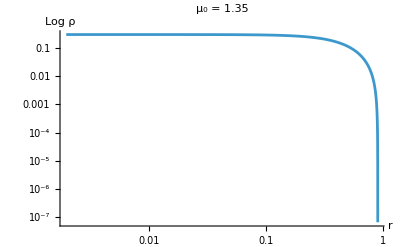
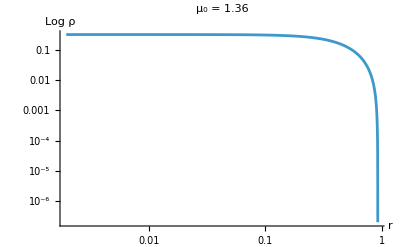
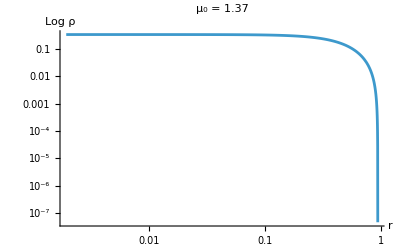
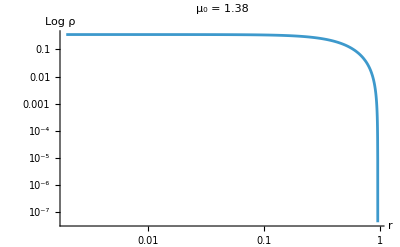
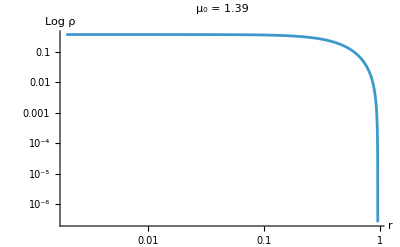
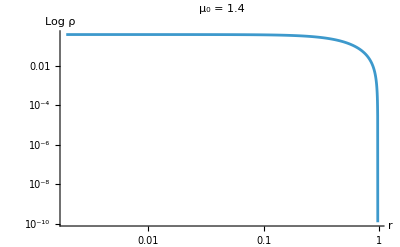
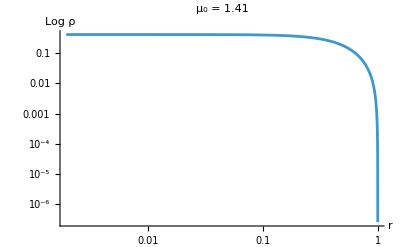
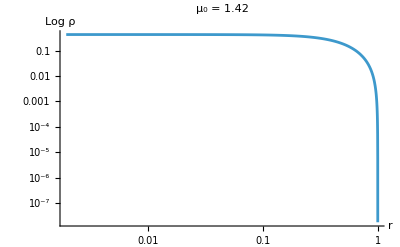

```mathematica
(* Full obtained density profiles (from r=0 up to r=Subscript[r, f]) *)
ρfull=Table[Piecewise[{{Normal[sρv[[i]]]/.rbackground[[i]],0≤r≤ri[[i]]},{Evaluate[ρ[μ[r][[i]]]/.Solution[[i]]],ri[[i]]<=r≤rf}}],{i,Nμ0}]  ;
(* PLOTS *)
Table[LogLogPlot[Evaluate[ρfull[[i]]],{r,0,rf},PlotLabel->"μ_0 = "<>ToString[N[μ0p[[i]]]],AxesLabel->{"r","Log ρ"},PlotRange->All],{i,Nμ0}]
```

#### Mass & Charge plots

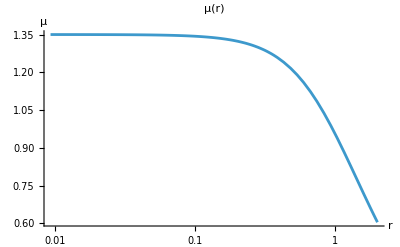
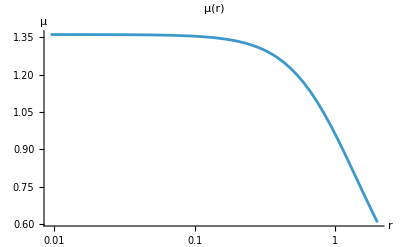
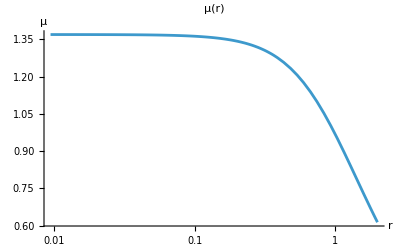
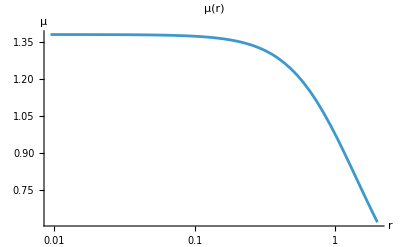
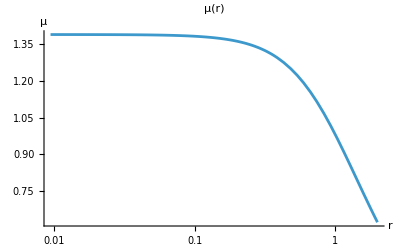
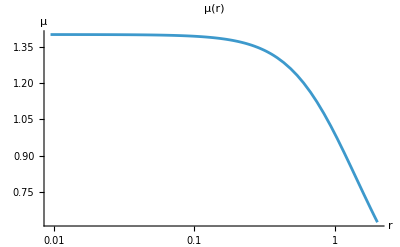
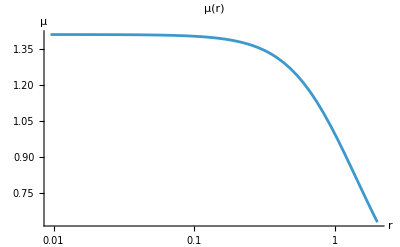
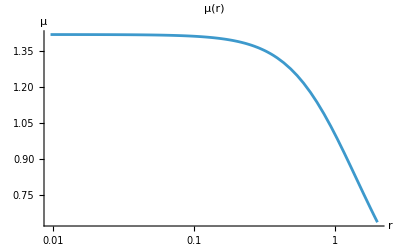

R = {0.906586,0.921019,0.935277,0.949362,0.963277,0.977026,0.990611,1.00403,1.01729,1.03039,1.04333,1.05612,1.06874,1.08121,1.09352,1.10567}

```mathematica
(* Full local chemical potential plots *)
μfull=Table[Piecewise[{{Normal[sμ[r,μ0p[[i]]]]/.rbackground[[i]],0≤r<ri[[i]]},{μ[r][[i]]/.Solution[[i]],ri[[i]]<=r≤rf}}],{i,Nμ0}] ;
Table[LogLinearPlot[μfull[[i]],{r,ri[[i]],rf},PlotRange->All,PlotLabel->"μ(r)",AxesLabel->{"r","μ"}],{i,Nμ0}]

(* Identification of the Star radius R where it finishes at T=0 *)
Rs=Table[r/.FindRoot[(μ[r][[i]]/.Solution[[i]])==1,{r,rf}],{i,Nμ0}] ; 
"R = "<>ToString[Rs,TraditionalForm]
```

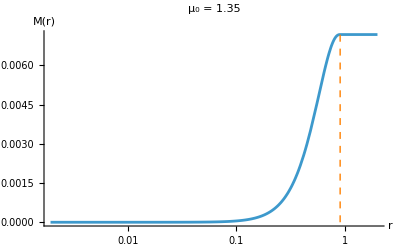
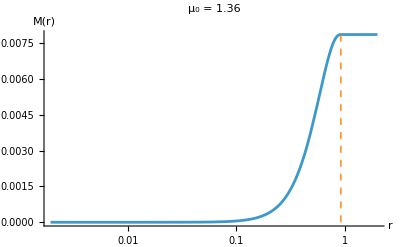
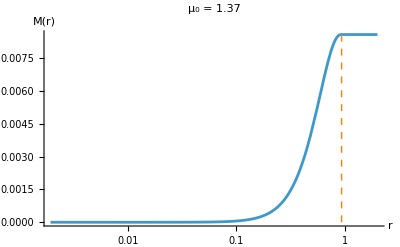
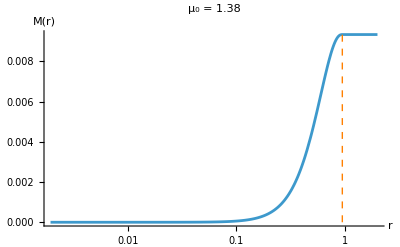
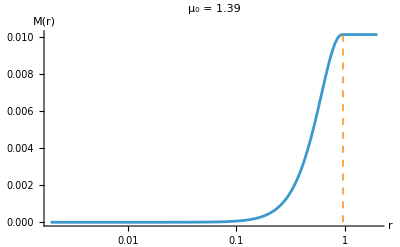
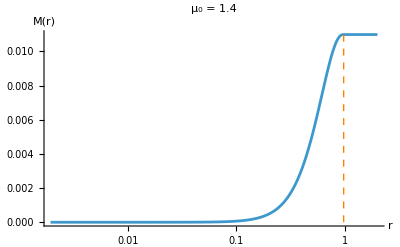
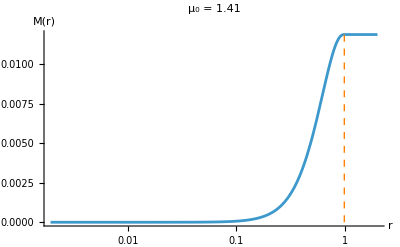
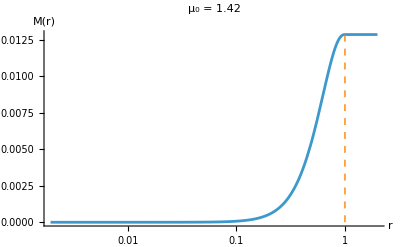
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Full Mass profiles plots (from r=0 to r=Subscript[r, f]) with the obtained Star radius R (dash orange line) *)
Ms=M[rf]/.Solution ;
Table[Show[LogLinearPlot[Piecewise[{{pM[r][[i]],0<=r≤ri[[i]]},{M[r]/.Solution[[i,1]],ri[[i]]<r<=rf}}],{r,0,rf},PlotLabel->"μ_0 = "<>ToString[N[μ0p[[i]]]],AxesLabel->{"r","M(r)"},PlotRange->All],Graphics[{Orange,Dashed,Line[{{Log[Rs[[i]]],0},{Log[Rs[[i]]],Ms[[i]]}}]}]],{i,Nμ0}]
```

```mathematica
(* Full Charge profiles plots (from r=0 to r=Subscript[r, f]) with the obtained Star radius R (dash orange line) *)
χs=χ[rf]/.Solution ; 
Qs=Exp[-χ[rf]/2]h'[rf] rf^2/.Solution ;
Table[Show[LogLinearPlot[Piecewise[{{Exp[-(pχ[r][[i]])/2]ph'[r][[i]] r^2,0<=r≤ri[[i]]},{Exp[-χ[r]/2]h'[r] r^2/.Solution[[i]],ri[[i]]<r<=rf}}],{r,0,rf},PlotLabel->"μ_0 = "<>ToString[N[μ0p[[i]]]],AxesLabel->{"r","Q(r)"},PlotRange->All],Graphics[{Orange,Dashed,Line[{{Log[Rs[[i]]],0},{Log[Rs[[i]]],Qs[[i]]}}]}]],{i,Nμ0}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Free Energy & Katz

```mathematica
(* Identifing the boundary chemical potential Subscript[μ, ∞]  *)
h∞=Table[D[r Solution[[i,2,2]][r],r]/.r->rf,{i,Nμ0}] ; 
μ∞=Table[Exp[-χs[[i]]/2](μ0p[[i]]+h∞[[i]]),{i,Nμ0}] ;  
(* Free energy of the Star *)
Wstar∞=Table[{μ∞[[i]],4π Exp[χs[[i]]/2](2Ms[[i]]-Qs[[i]]μ∞[[i]])},{i,Nμ0}]; 
(* Free energy of the Large BH *)
WBH∞[μBH_]=-2/3 √(2/3) π (-2+μBH^2)^(3/2) ;

(* Free energy of the TAdS *)
WAdST∞[TAdS_]=0 ;
```

```mathematica
(* Plot of the Free energy of the Star, BH and TAdS, for the obtained range of the boundary chemical potential Subscript[μ, ∞] *)
μBHi=TakeSmallest[Table[μ∞[[i]],{i,Nμ0}],1][[1]] ; μBHf=TakeLargest[Table[μ∞[[i]],{i,Nμ0}],1][[1]] ;
Show[ListPlot[{Wstar∞},AxesLabel->{"μ_∞","W"},PlotStyle->{Blue,Black},PlotRange->All,PlotLegends->{"Electron Star","Black Hole"},PlotLabel->"Free Energy with T = 0"],Plot[{WAdST∞[μBH],WBH∞[μBH]},{μBH,μBHi,μBHf},PlotLegends->{"Thermal AdS","Black Hole"},PlotStyle->{Orange,Black},PlotRange->All]]
```

-Graphics-

```mathematica
(* Relation between the chosen central chemical potential Subscript[μ, 0] and the obtained boundary chemical potential Subscript[μ, ∞] *)
ListPlot[Table[{μ0p[[i]],μ∞[[i]]},{i,Nμ0}],AxesLabel->{"μ_0","μ_∞"},PlotRange->All,PlotLabel->"μ_∞(μ_0)",PlotStyle->Blue]
```

-Graphics-

```mathematica
(* At T=0 we can not use Katz as a plot of the Mass and β, but we can use the charge and the chemical potential *)
katz=Table[{μ∞[[i]],Qs[[i]]},{i,Nμ0}]  ;
ListPlot[katz,AxesLabel->{"μ_∞","Q_s"},PlotRange->All,PlotLabel->"Stability: Katz Criteria",PlotStyle->Blue]
```

-Graphics-